```mathematica
ClearAll["Global`*"]
```

```mathematica
Mpl=1.0;                 (* reduced mass Planck *)
mϕ=1.0;                   (* inflation mass *)
λ=0.0;                     (* self-coupling constant *)
g=200.0;                 (* coupling constant ϕ-χ *)
tMax=50.0;            (* Time *)
ϕ0=0.1 Mpl;           (* Initial amplitude ϕ *)


q = (g^2 ϕ0^2)/(4 mϕ^2);               (* Resonant parameter *)
A[k_] := k^2/mϕ^2+2q;
```

```mathematica
(* Background equations: EOM Inflaton field, Friedman equation *)
H[ϕ_,dϕ_]:=√(1/(3 Mpl^2)(1/2 dϕ^2 + 1/2 mϕ^2 ϕ^2+ λ/4 ϕ^4))
eqa = a'[t]==a[t]*H[ϕ[t],ϕ'[t]];
eqϕ=ϕ''[t]+3H[ϕ[t],ϕ'[t]]ϕ'[t]+mϕ^2 ϕ[t]+λ ϕ[t]^3==0;

(*Initial conditions*)
backgroundconditions = {a[0]==1,ϕ[0]==ϕ0,ϕ'[0]==0};

(* Solve Background dynamic *)
solbackground=NDSolve[{eqϕ,eqa,backgroundconditions[[1]],backgroundconditions[[2]],backgroundconditions[[3]]},{ϕ,a},{t,0,tMax},MaxSteps->100000];

(* Solution's background *)
ϕsol[t_]:=Evaluate[ϕ[t]/. solbackground[[1]]];
asol[t_]:=Evaluate[a[t]/. solbackground[[1]]];
Hsol[t_]:=H[ϕsol[t],ϕsol'[t]];
```

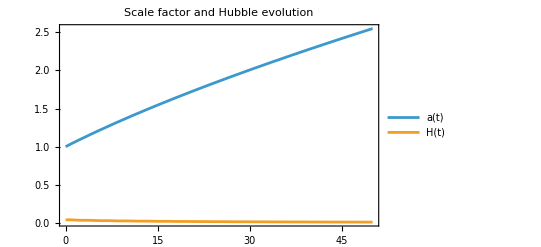

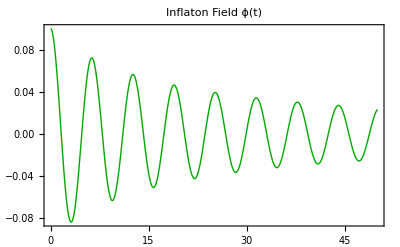

```mathematica
(*Plots *)
Plot[{asol[t],Hsol[t]},{t,0,tMax},PlotRange->All,PlotLegends->{"a(t)","H(t)"},Frame->True,PlotLabel->"Scale factor and Hubble evolution"]
Plot[ϕsol[t],{t,0,tMax},PlotRange->All,PlotStyle->{Thick,Darker[Green]},Frame->True,PlotLabel->"Inflaton Field ϕ(t)"]
```

```mathematica
kvalues= 10^Subdivide[0,3,10];

(* Frequency *)
ω2[t_,k_]:=k^2+g^2 ϕsol[t]^2;
ω[t_,k_]:=√ω2[t,k];

(* EOM daughter χ *)
eqχ[k_]:=χ''[t]+ω2[t,k]*χ[t]==0;

For[i=1,i<=Length[kvalues],i++,
(* Initial conditions  to be valued at  *)
χconditions={χ[0]==1/(√(2ω[0,kvalues[[i]]])),χ'[0]==-I*√(ω[0,kvalues[[i]]]/2)}; 
(*Solve χ dynamic *)
solχ = NDSolve[{eqχ[kvalues[[i]]],χconditions[[1]],χconditions[[2]]},χ,{t,0,tMax},MaxSteps->Infinity,Method->"StiffnessSwitching"];

(* Solution χ *)
χsol[t_]:=Evaluate[χ[t]/. solχ[[1]]];

(* Number particles *)
numbχ[t_]:=1/2 Abs[χ'[t]]^2/ω[t,kvalues[[i]]]+ω[t,kvalues[[i]]]/2 Abs[χ[t]]^2-1/2;
numbχsol[t_]:=Evaluate[numbχ[t]/. solχ[[1]]];

χPlot = Plot[Re[χsol[t]],{t,0,tMax},PlotRange->All,PlotStyle->{Thick ,Blue},Frame->True,FrameLabel->{"Time (t)","χ_k"},PlotLabel->StringForm["Daughter field Re[χ_k] for ``",kvalues[[i]]]];
nPlot= nPlot[numbχsol[t],{t,0,tMax},PlotRange->All,PlotStyle->{Thick,Red},Frame->True,FrameLabel->{"Time (t)","n_k"},PlotLabel->StringForm["Number density n_k for ``",kvalues[[i]]]];

GraphicsRow[{χPlot,nPlot}]
];
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.